```mathematica
Module[{},
Clear[SIMNOTPERFECTMODEL,FASTTRAJECTORY,ESTIMATESENSITIVITY,SIMTIMEVARYINGWIND,ESTIMATESENSITIVITY2,FASTTRAJECTORY2];
If[#==1,
(*option 1*)
nameSIM="default"
];
If[#==2,
(*option 2*)
SIMNOTPERFECTMODEL=True;
nameSIM="model mismatch";
];
If[#==3,
(*option 3*)
FASTTRAJECTORY=True;
nameSIM="fast trajectory";
];
If[#==4,
(*option 4*)
ESTIMATESENSITIVITY=True;
nameSIM="estimate sensitivity";
];

If[#==5,
(*option 5*)
SIMTIMEVARYINGWIND=True;
nameSIM="time varying wind";
];

If[#==6,
(*option 6*)
ESTIMATESENSITIVITY2=True;
nameSIM="estimate sensitivity 2";
];

If[#==7,
(*option 7*)
FASTTRAJECTORY2=True;
nameSIM="fast trajectory 2";
];

If[#==8,
(*option 6*)
ESTIMATESENSITIVITY3=True;
nameSIM="estimate sensitivity 3";
];
]&[4]
nameSIM
```

estimate sensitivity

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"model_and_change_of_coordinates.nb"}]]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"backstepping_steps.nb"}]]
(*Play[Sin[440 2Pi t],{t,0,1}](*Beep[]*)*)
```

```mathematica
SIMFULLY=True;
SIMUNDER=False;
(*run everything*)
COMMENT=False;
(*some parts are not run: creation of pictures, and some other things I only needed to do once*)
(*COMMENT=True;*)
```

# controller for original system (after backstepping): fully-actuated

computing dω_2(x3) is very expensive, and I am computing it several times, the way it is formulated in the backstepping notebook

for that reason I am defining an auxiliary function that will prevent me from computing dω_2(x3) three times

## generate random estimates inside bounds

```mathematica
estimatorsRandom[]:=Module[{
random=Function[bound,#1/(√(#1.#1+#2^2))&[RandomReal[{-bound,bound},3],bound]]
},
Module[{
bT=random[θ0bT+ϵbT/.EstimatorsParameters],
BT=random[θ0BT+ϵBT/.EstimatorsParameters],
bτ=random[θ0bτ+ϵbτ/.EstimatorsParameters],
Bτ=random[θ0Bτ+ϵBτ/.EstimatorsParameters],
},
Join[bT,BT,bτ,Bτ]
]
];
estimatorsRandom[]
```

{0.234097,-0.276267,0.57878,-0.400242,0.0872171,0.644329,-0.324217,0.14325,-0.498508,-0.114808,-0.358904,-0.532712}

## torque control law (auxiliary function)

```mathematica
τ1clAUXILIAR[x5_,b_,B_,{ω0d_,dω_}]:=Module[{
p=x5[[1;;3]],
v=x5[[4;;6]],

g0=x5[[7;;9]],
n=x5[[10;;12]],

bT=x5[[16;;18]],
BT=x5[[19;;21]],
ω=x5[[22;;24]],
g2=x5[[25;;27]],

x2=x5[[1;;15]],
x3=x5[[1;;18]],
x4=x5[[1;;21]]
},
Module[{
d0uDI=Evaluate[uDIChosen[p,v]],

(*ω0d=Evaluate[ω2cl[x3]],*)
(*dω=Evaluate[dω2cl[x3]],*)
(*dω=Transpose[Table[D[ω2cl[ReplacePart[x3,i->x]],x]/.{x->x3[[i]] },{i,Range[18]}]],*)

VV=Evaluate[Subscript[V, 2][x2,bT]]

},
Module[{
ω1d=Evaluate[dω.X3[x3,Join[{T3cl[x4]},ω,g2],b,B]/.Controllers],
 y0d=Evaluate[g0+d0uDI-bT]
},
Module[{
(*∂/(∂n)Subscript[V, 2][x2,bT]*)
dVV=Evaluate[(γθ/.Controllers) ((y0d/(√(y0d.y0d))).Skew[n])]
},
(*NOTE: ω0d is orthogonal to n, but ω1d is not necessarily*)
AngularAcceleration[
ω(*angular velocity*),
{ω0d,OP[n].ω1d}(*desired angular velocity and its time derivative*),
{VV,dVV}/.Controllers,
{kpω,γω,Subscript[V, 2,0]}/.Controllers
]+OP[n].(-ϕτ[n].B)/.Controllers
(*REMARK BELOWWWWWWWW*)
(*NOT CORRECT: the other terms!!!!!!OP[n].(-ϕτ[n].B+(dω[[;;,{4,5,6}]]).(n ϕT[n].(B-BT) + (b-bT)))//.Controllers*)
]
]
]
]
(*test*)
x5Random=x5R[];
If[!COMMENT,Timing[τ1cl[x5Random,b/.PhysicalConstants,B/.PhysicalConstants]]]
ω2clRandom=ω2cl[x5Random[[1;;18]]];
dω2clRandom=Transpose[Table[D[ω2cl[ReplacePart[#,i->x]],x]/.{x->#[[i]] },{i,Range[18]}]]&[x5Random[[1;;18]]];
If[!COMMENT,Timing[τ1clAUXILIAR[x5Random,b/.PhysicalConstants,B/.PhysicalConstants,{ω2clRandom,dω2clRandom}]]]
```

{0.884,{-15.3285,13.6395,8.15643}}

{0.008,{-15.3285,13.6395,8.15643}}

## compare which method is faster

```mathematica
derivativeAUX[function_,x2_,bT_]:=Module[{
xlocal
},
Join[
Evaluate[
Transpose[
Table[
D[
function[ReplacePart[x2,i->xlocal], bT],
xlocal
]/.{xlocal->x2[[i]] },
{i,Range[x2Dim]}
]
]
]
,
Evaluate[
Transpose[
Table[
D[
function[x2, ReplacePart[bT,i->xlocal]],
xlocal
]/.{xlocal->bT[[i]] },
{i,Range[3]}
]
]
]
,
2
]
];
```

```mathematica
x3Random=x3R[];
(*x3Random=Join[x3Random[[1;;x2Dim]],{0.1,0.1,0.1}];*)
dω2cl[x3_]:=Module[{
xlocal
},Evaluate[Transpose[Table[D[ω2cl[ReplacePart[x3,i->xlocal]],xlocal]/.{xlocal->x3[[i]] },{i,Range[18]}]]]//N
]
sol1=dω2cl[x3Random]//Timing;

dω2cl[x3_]:=Module[{
xlocal,
x2=x3[[1;;x2Dim]],
bT=x3[[-3;;-1]],

bTdot, dbTdot
},
(*ω2cl=ω1cl[x2,bT,bTdot]*)
If[(bT.bT-θ0bT^2/.Estimators)≤ 0,
bTdot=Evaluate[
DiagonalMatrix[kibT/.Estimators].XbTChosenFast[x2,bT]/.Estimators
];
dbTdot=derivativeAUX[DiagonalMatrix[kibT/.Estimators].XbTChosenFast[#1,#2]&,x2,bT];
,
bTdot=Evaluate[
EstimatorProj2
[DiagonalMatrix[kibT/.Estimators].XbTChosenFast[x2,bT],bT,{θ0bT,ϵbT,δbT,nbT}
]/.Estimators
];
dbTdot=derivativeAUX[
(EstimatorProj2[DiagonalMatrix[kibT/.Estimators].XbTChosenFast[#1,#2],#2,{θ0bT,ϵbT,δbT,nbT}
]/.Estimators)&,x2,bT
];
];
derivativeAUX[ω1cl[#1,#2,bTdot]&,x2,bT]+Transpose[
Table[
D[
ω1cl[x2,bT, ReplacePart[bTdot,i->xlocal]],
xlocal
]/.{xlocal->bTdot[[i]] },
{i,Range[3]}
]
].dbTdot
]
sol2=dω2cl[x3Random]//Timing;

dω2cl[x3_]:=Module[{
xlocal,
x2=x3[[1;;x2Dim]],
bT=x3[[-3;;-1]],

bTdot,bTdotAUX,dbTdot,dbTdotAUX
},
(*ω2cl=ω1cl[x2,bT,bTdot]*)

bTdotAUX=Evaluate[
DiagonalMatrix[kibT/.Estimators].XbTChosenFast[x2,bT]/.Estimators
];
dbTdotAUX=derivativeAUX[DiagonalMatrix[kibT/.Estimators].XbTChosenFast[#1,#2]&,x2,bT];
If[(bT.bT-θ0bT^2/.Estimators)≤ 0,
(*unchanged*)
bTdot=bTdotAUX;
dbTdot=dbTdotAUX;
,
bTdot=Evaluate[EstimatorProj2[bTdotAUX,bT,{θ0bT,ϵbT,δbT,nbT}/.Estimators]];
dbTdot=d1EstimatorProj2[bTdotAUX,bT,{θ0bT,ϵbT,δbT,nbT}/.Estimators].dbTdotAUX+Join[
ConstantArray[0,{3,x2Dim}],
d2EstimatorProj2[bTdotAUX,bT,{θ0bT,ϵbT,δbT,nbT}/.Estimators],
2];
];
derivativeAUX[ω1cl[#1,#2,bTdot]&,x2,bT]+Transpose[
Table[
D[
ω1cl[x2,bT, ReplacePart[bTdot,i->xlocal]],
xlocal
]/.{xlocal->bTdot[[i]] },
{i,Range[3]}
]
].dbTdot
]
sol3=dω2cl[x3Random]//Timing;

(*sol1[[1]]/sol2[[1]]*)
(*sol2[[1]]/sol3[[1]]*)
sol1[[1]]
sol2[[1]]
sol3[[1]]
sol1[[2]]-sol2[[2]]//Chop
sol1[[2]]-sol3[[2]]//Chop
```

0.88

0.152

0.144

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

## Input and update-laws combined

```mathematica
InputAndUpdateLaws[t_,z_,controllerState_]:=Module[{
(*from z to x*)
(*x = (p,v,n,ω)*)
x=f[z,Evaluate[{pd[t],vd[t]}]]/.Controllers//N,

bT=controllerState[[1;;3]],
BT=controllerState[[4;;6]],
bτ=controllerState[[7;;9]],
Bτ=controllerState[[10;;12]],

g0=Evaluate[gravity{0,0,1}+ad[t]/.Controllers]//N,
g1=Evaluate[jd[t]]//N,
g2=Evaluate[sd[t]]//N,

V6, W6
},
Module[{
p=x[[1;;3]]//N,
v=x[[4;;6]]//N,
n=x[[7;;9]]//N,
ω=x[[10;;12]]//N
},
Module[{
(*x1=Evaluate[Join[p,v,g0]]//N,*)
x2=Evaluate[Join[p,v,g0,n,g1]]//N,
x3 =Evaluate[Join[p,v,g0,n,g1,bT]]//N,
x4 =Evaluate[Join[p,v,g0,n,g1,bT,BT]]//N,
x5 =Evaluate[Join[p,v,g0,n,g1,bT,BT,ω,g2]]//N,
x6 =Evaluate[Join[p,v,g0,n,g1,bT,BT,ω,g2,bτ,Bτ]]//N,
ν,u
},
Module[{
ωcl=Evaluate[ω2cl[x3]]//N,
dωcl=dω2cl[x3],
(*dωcl=Evaluate[Transpose[Table[D[ω2cl[ReplacePart[x3,i->xlocal]],xlocal]/.{xlocal->x3[[i]] },{i,Range[18]}]]]//N,*)
(*dωcl=RandomReal[{-2,2},{3, x3Dim}],*)

XbτChosenFast,XBτChosenFast,

bTdot,BTdot,bτdot,Bτdot,
zdot
},

ν=Join[{T3cl[x4]},τ1clAUXILIAR[x5,bτ,Bτ,{ωcl,dωcl}]];
u=uϕ[Join[p,v,n,ω],ν]/.Controllers;


bTdot=EstimatorProj[DiagonalMatrix[kibT].XbTChosenFast[x2,bT],bT,{θ0bT,ϵbT,δbT,nbT}]/.ControllersWithEstimators;
BTdot=EstimatorProj[DiagonalMatrix[kiBT].XBTChosenFast[x3,BT],BT,{θ0BT,ϵBT,δBT,nBT}]/.ControllersWithEstimators;

XbτChosenFast=γω(ω-ωcl).(-#)&[dωcl[[;;,{4,5,6}]]]/.Controllers//N;
bτdot=EstimatorProj[kibτ XbτChosenFast,bτ,{θ0bτ,ϵbτ,δbτ,nbτ}]/.Estimators//N;
XBτChosenFast=γω(ω-ωcl).(ϕτ[n]-KroneckerProduct[#.n, ϕT[n]])&[dωcl[[;;,{4,5,6}]]]/.Controllers//N;
Bτdot=EstimatorProj[kiBτ XBτChosenFast,Bτ,{θ0Bτ,ϵBτ,δBτ,nBτ}]/.Estimators//N;

V6=Subscript[V, 6][x6 ,b/.PhysicalConstants,B/.PhysicalConstants];
(*the one below takes too long: because it recomputes dωcl*)
(*W6=Subscript[W, 6][x6 ,b/.PhysicalConstants,B/.PhysicalConstants];*)
W6=Subscript[W, 5][x5 ,b/.PhysicalConstants,B/.PhysicalConstants]-(((b/.PhysicalConstants)-bτ).(bτdot-kibτ XbτChosenFast))/kibτ-(((B/.PhysicalConstants)-Bτ).(Bτdot-kiBτ XBτChosenFast))/kiBτ/.ControllersWithEstimators;

{u,Join[bTdot,BTdot,bτdot,Bτdot],V6,W6}

]
]
]
]
(*zR[] -- see "model_and_change_of_coordinates.nb"*)
(*If[!COMMENT,InputAndUpdateLaws[RandomReal[{-2,2}],zR[],RandomReal[{-2,2},12]]//Timing]*)
If[!COMMENT,InputAndUpdateLaws[RandomReal[{-2,2}],zR[],estimatorsRandom[]]//Timing]
```

{0.2,{{-21.8966,9.34931,91.5105},{-0.145808,-0.0783699,-0.0798411,-0.168996,-0.0436841,0.120721,0.186411,-0.0158674,0.877985,-2.6682,-1.81065,-3.9337},661.255,-6246.56}}

### faster computing at equilibrium

```mathematica
zeq[t_]:=Join[
pd[t],
vd[t],
#1/(√(#1.#1)),
Skew[#1/(√(#1.#1))].(#2/(√(#1.#1)))
]&[gravity{0,0,1}+ad[t]-b/.PhysicalConstants,jd[t]]
zeq[RandomReal[]]
If[!COMMENT,InputAndUpdateLaws[#,zeq[#],Join[b,B,b,B]/.PhysicalConstants]&[RandomReal[]]//Timing]
```

{0.723885,1.44771,0.911353,0.51273,-0.639119,-0.561833,-0.161763,-0.0721463,0.984189,-0.178719,-0.00413874,-0.029678}

{0.184,{{46.0428,-77.6114,139.243},{-0.0607475,-0.880458,0.306562,0.95812,-3.66368,-3.45742,-5.23585,4.07138,-1.68081,-4.47506,7.89057,5.6857},58.8297,-557.562}}

## confirm all is correct with Lyapunov function

## Lyapunov function: V

```mathematica
Subscript[VModified, 6][t_,z_,estimators_,winds_]:=Module[{
ww =winds[[1;;3]],
WW =winds[[4;;6]],

x=f[z,Evaluate[{pd[t],vd[t]}]]/.Controllers//N,

bT=estimators[[1;;3]],
BT=estimators[[4;;6]],
bτ=estimators[[7;;9]],
Bτ=estimators[[10;;12]],

g0=Evaluate[gravity{0,0,1}+ad[t]/.Controllers]//N,
g1=Evaluate[jd[t]]//N,
g2=Evaluate[sd[t]]//N,

x6
},
Module[{
p=x[[1;;3]],
v=x[[4;;6]],
n=x[[7;;9]],
ω=x[[10;;12]]
},

x6=Evaluate[Join[p,v,g0,n,g1,bT,BT,ω,g2,bτ,Bτ]];
Subscript[V, 6][x6,ww/m,WW/M-ww/m/.PhysicalConstants]
]
]
(*test*)
If[!COMMENT,
Subscript[VModified, 6][1,zR[]/.PhysicalConstants,RandomReal[{-2,2},12],{w1,w2,w3,W1,W2,W3}/.PhysicalConstants]
]
```

202.017

## Lyapunov function time derivative: W

```mathematica
Subscript[WModified, 6][t_,z_,estimators_,winds_]:=Module[{
ww =winds[[1;;3]],
WW =winds[[4;;6]],

x=f[z,Evaluate[{pd[t],vd[t]}]]/.Controllers//N,

bT=estimators[[1;;3]],
BT=estimators[[4;;6]],
bτ=estimators[[7;;9]],
Bτ=estimators[[10;;12]],

g0=Evaluate[gravity{0,0,1}+ad[t]/.Controllers]//N,
g1=Evaluate[jd[t]]//N,
g2=Evaluate[sd[t]]//N,

x6
},
Module[{
p=x[[1;;3]],
v=x[[4;;6]],
n=x[[7;;9]],
ω=x[[10;;12]]
},

x6=Evaluate[Join[p,v,g0,n,g1,bT,BT,ω,g2,bτ,Bτ]];
Subscript[W, 6][x6,ww/m/.PhysicalConstants,WW/M-ww/m/.PhysicalConstants]
]
]
(*test*)
(*If[!COMMENT,
Subscript[WModified, 6][RandomReal[],zR[]/.PhysicalConstants,RandomReal[{-2,2},12],{w1,w2,w3,W1,W2,W3}/.PhysicalConstants]
]*)
If[!COMMENT,
Subscript[WModified, 6][RandomReal[],zR[]/.PhysicalConstants,estimatorsRandom[],{w1,w2,w3,W1,W2,W3}/.PhysicalConstants]
]
```

-2713.01

## check V̇=W

```mathematica
error[t_,z_,estimators_]:=Module[{
winds={w1,w2,w3,W1,W2,W3}/.PhysicalConstants,
input,estimatorsUpdate,zdot,
d1V,d2V,d3V,
V6,W6
},
{input,estimatorsUpdate,V6,W6}=InputAndUpdateLaws[t,z,estimators];
zdot=Z[z,input,gravity{0,0,1},winds]/.PhysicalConstants;
d1V=D[Subscript[VModified, 6][tt,z,estimators,winds],tt]/.{tt-> t};
d2V=Evaluate[Array[D[Subscript[VModified, 6][t,ReplacePart[z,#->x],estimators,winds],x]/.{x->z[[#]]}&,12]].zdot;
d3V=Evaluate[Array[D[Subscript[VModified, 6][t,z,ReplacePart[estimators,#->x],winds],x]/.{x->estimators[[#]] }&,12]].estimatorsUpdate;
d1V+d2V+d3V-Subscript[WModified, 6][t,z,estimators,winds]
]
(*If[!COMMENT,
error[RandomReal[],zR[]/.PhysicalConstants,RandomReal[{-2,2},12]]//Chop
]*)
If[!COMMENT,
error[RandomReal[],zR[]/.PhysicalConstants,estimatorsRandom[]]//Chop
]
```

0

## generate state x_6 from time instant, system state, and controller state

```mathematica
f6[t_,z_,ξ_]:=Module[{
x=f[z,Evaluate[{pd[t],vd[t]}]]/.Controllers//N,

bT=ξ[[1;;3]],
BT=ξ[[4;;6]],
bτ=ξ[[7;;9]],
Bτ=ξ[[10;;12]],

g0=Evaluate[gravity{0,0,1}+ad[t]/.Controllers]//N,
g1=Evaluate[jd[t]]//N,
g2=Evaluate[sd[t]]//N,
},
Module[{
p=x[[1;;3]],
v=x[[4;;6]],
n=x[[7;;9]],
ω=x[[10;;12]]
},
(*x6*)
Evaluate[Join[p,v,g0,n,g1,bT,BT,ω,g2,bτ,Bτ]
]
]
]
f6[RandomReal[],zR[]/.PhysicalConstants,estimatorsRandom[]]
Subscript[V, 6][f6[RandomReal[],zR[]/.PhysicalConstants,estimatorsRandom[]],b,B]/.PhysicalConstants
(*the one below is taking too long*)
(*Subscript[W, 6][f6[RandomReal[],zR[]/.PhysicalConstants,estimatorsRandom[]],b,B]/.PhysicalConstants*)
Subscript[W, 5][f6[RandomReal[],zR[]/.PhysicalConstants,estimatorsRandom[]][[1;;x5Dim]],b,B]/.PhysicalConstants
```

{2.91395,0.47534,8.71802,-10.2453,-0.330911,5.64169,-0.681403,-1.38815,9.51329,0.662893,0.508521,-0.549527,-1.91596,1.14982,1.52196,-0.391977,0.069343,-0.572567,0.586092,0.282348,0.462782,-2.83093,-2.65842,-5.87498,4.28936,4.61098,-0.0567987,0.579889,-0.0712095,-0.297195,-0.627494,-0.431829,-0.0630845}

283.753

-2588.04

## equilibrium z^*, u^*, and verifying (ż)^*=Z(z^*,u^*)

### z^*

```mathematica
zstartrajectory[t_]:=Join[
pd[t],
pd[t]+l#/(√(#.#))&[m gravity{0,0,1}+m ad[t]-{w1,w2,w3}],
vd[t],
vd[t]+l OP[#1/(√(#1.#1))].(#2/(√(#1.#1)))&[m gravity{0,0,1}+m ad[t]-{w1,w2,w3},m jd[t]]
]
zstartrajectoryDEF[t_]=zstartrajectory[t]/.PhysicalConstants;
timeRandom=RandomReal[];
zstartrajectory[timeRandom]/.PhysicalConstants//Timing
zstartrajectoryDEF[timeRandom]//Timing
```

{0.004,{0.833524,1.21523,0.746535,0.668218,1.19083,1.83377,0.184037,-0.797769,-0.466695,0.256653,-0.658021,-0.452518}}

{0.008,{0.833524,1.21523,0.746535,0.668218,1.19083,1.83377,0.184037,-0.797769,-0.466695,0.256653,-0.658021,-0.452518}}

### u^*

```mathematica
(*ustartrajectory[t_]:=
((M D[#[[10;;12]],tt]+m D[#[[7;;9]],tt]/.{tt-> t})+(M+m)gravity{0,0,1}-({W1,W2,W3}+{w1,w2,w3}))&[zstartrajectory[tt]]*)
ustartrajectory[t_]:=
Evaluate[(D[M #[[10;;12]]+m #[[7;;9]]&[zstartrajectory[tt]],tt]/.{tt-> t})+(M+m)gravity{0,0,1}-({W1,W2,W3}+{w1,w2,w3})]
ustartrajectoryDEF[t_]:=Evaluate[ustartrajectory[t]/.PhysicalConstants]

timeRandom=RandomReal[];
ustartrajectory[timeRandom]/.PhysicalConstants//Timing
ustartrajectoryDEF[timeRandom]//Timing
```

{0.028,{-2.30832,-1.41067,15.1803}}

{0.024,{-2.30832,-1.41067,15.1803}}

### (ż)^*=Z(z^*,u^*) this must be satisfied

```mathematica
error[t_]:=(D[zstartrajectory[tt],tt]/.{tt-> t})-Z[zstartrajectory[t],ustartrajectory[t],gravity{0,0,1},{w1,w2,w3,W1,W2,W3}]
error[RandomReal[]]/.PhysicalConstants//Chop//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0}

## Simulation

```mathematica
(*TFINAL=35;
stepsize=0.005;
computationtime=0.18;
(computationtime TFINAL/stepsize)/(60 60)*)
```

```mathematica
(*initial state*)
z0=Join[
If[ESTIMATESENSITIVITY||ESTIMATESENSITIVITY2||ESTIMATESENSITIVITY3,{20,20,20},{7,7,7}],(*p*)
If[ESTIMATESENSITIVITY||ESTIMATESENSITIVITY2||ESTIMATESENSITIVITY3,{20,20,20},{7,7,7}]+l{0,0,1},(*P*)
If[ESTIMATESENSITIVITY||ESTIMATESENSITIVITY2||ESTIMATESENSITIVITY3,{5,5,5},{0,0,0}],(*v*)
If[ESTIMATESENSITIVITY||ESTIMATESENSITIVITY2||ESTIMATESENSITIVITY3,{5,5,5},{0,0,0}](*V*)
]/.PhysicalConstants//N;
Projz[#]-#&[z0]/.PhysicalConstants//Chop
(*initial estimators*)
estimators0=ConstantArray[0,12];
```

{0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
TFINAL=35;
stepsize=0.005;
NN=Round[TFINAL/0.005];

If[SIMFULLY,


stateList={};
estimatorsList={};
stateStarList={};
inputStarList={};
tensionsList={};

inputList ={};
VList ={};
WList ={};

kk=1;
i0=1;
For[i=i0,i<=NN,i++,
time=stepsize(i-1);

winds=({w1,w2,w3,W1,W2,W3}/.PhysicalConstants)+If[ValueQ[SIMTIMEVARYINGWIND],{0.15 Sin[(2π)/4 time],0,0,0.15 Sin[(2π)/4 time],0,0},{0,0,0,0,0,0}] ;

{input,estimatorsUpdate,V6,W6}=InputAndUpdateLaws[time,z0,estimators0];
z0=Projz[z0+stepsize Z[z0,input,gravity{0,0,1},winds]]/.PhysicalConstants;
estimators0=estimators0+stepsize estimatorsUpdate;

stateList= Join[stateList,{z0}];
estimatorsList= Join[estimatorsList,{estimators0}];
inputList= Join[inputList,{input}];

stateStarList= Join[stateStarList,{zstartrajectory[time]/.PhysicalConstants}];
inputStarList= Join[inputStarList,{ustartrajectory[time]/.PhysicalConstants}];
tensionsList= Join[tensionsList,{Tension[z0,input,gravity{0,0,1},winds]/.PhysicalConstants}];


VList= Join[VList,{V6}];
WList= Join[WList,{W6}];

If[i≥500 kk,Play[Sin[440 2Pi t],{t,0,1}](*Beep[]*);Print[i];kk=kk+1];
]
]
Play[Sin[440 2Pi t],{t,0,1}]
Play[Sin[440 2Pi t],{t,0,1}]
Play[Sin[440 2Pi t],{t,0,1}]
Play[Sin[440 2Pi t],{t,0,1}]
```

500

1000

1500

2000

2500

3000

3500

4000

4500

5000

5500

6000

6500

7000

```mathematica
NN=Length[stateList];
XTicksLabels=Table[{Round[1/stepsize]i+1,i},{i,0,TFINAL,2}];
```

```mathematica
(*f6[TFINAL,stateList[[-1,;;]],estimatorsList[[-1,;;]]][[1;;3]]
XbTChosenFast[#[[1;;x2Dim]],#[[x2Dim+1;;x2Dim+3]]]&[f6[TFINAL,stateList[[-1,;;]],estimatorsList[[-1,;;]]]]

XbT[#[[1;;x2Dim]],#[[x2Dim+1;;x2Dim+3]]]&[f6[TFINAL,stateList[[-1,;;]],estimatorsList[[-1,;;]]]]/.Estimators*)
```

## saving data

```mathematica
If[SIMFULLY,
Export[NotebookDirectory[]<>"figures/fullyactuated/plot_trajectory_matlab/"<>nameSIM<>"/data_physical_constants.txt",ToString[Join[PhysicalConstants0,{timestep-> stepsize}]]];
Export[NotebookDirectory[]<>"figures/fullyactuated/plot_trajectory_matlab/"<>nameSIM<>"/data_state.mat",stateList];
Export[NotebookDirectory[]<>"figures/fullyactuated/plot_trajectory_matlab/"<>nameSIM<>"/data_state_star.mat",stateStarList];
Export[NotebookDirectory[]<>"figures/fullyactuated/plot_trajectory_matlab/"<>nameSIM<>"/data_input.mat",inputList];
Export[NotebookDirectory[]<>"figures/fullyactuated/plot_trajectory_matlab/"<>nameSIM<>"/data_input_star.mat",inputStarList];
]
```

### export

```mathematica
If[SIMFULLY,
Export[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_state.mx",stateList];
Export[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_estimators.mx",estimatorsList];
Export[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_input.mx",inputList];
Export[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_statestar.mx",stateStarList];
Export[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_inputstar.mx",inputStarList];
Export[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_tension.mx",tensionsList];
Export[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_V.mx",VList];
Export[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_W.mx",WList];
]
```

### Import

```mathematica
(*stateList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_state.mx"];
estimatorsList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_estimators.mx"];inputList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_input.mx"];
stateStarList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_statestar.mx"];
inputStarList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_inputstar.mx"];
tensionsList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_tension.mx"];
VList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_V.mx"];
WList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_W.mx"];
*)
```

## Error position

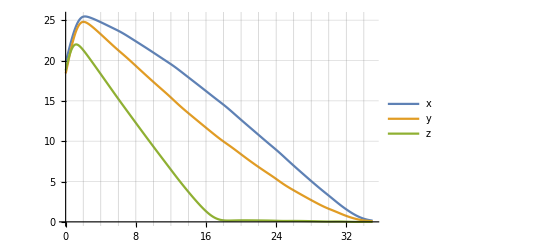
-Graphics-time (s)position error(m)

```mathematica
errorp:= stateList[[1;;NN,{1,2,3}]]-Table[pd[stepsize (i-1)],{i,1,Length[stateList[[;;,1]]]}];
If[SIMFULLY,
Labeled[
ListLinePlot[{
errorp[[;;,1]],errorp[[;;,2]],errorp[[;;,3]]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","position error(m)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMFULLY,Export[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/error_position.pdf",%];]
```

```mathematica
(*If[SIMFULLY,
Labeled[
ListLinePlot[{
errorp[[;;,1]],errorp[[;;,2]],errorp[[;;,3]]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->{-0.15,0.15}
],
{"time (s)","position error(m)"},{Bottom,Left},RotateLabel->True
]
]*)
```

## Error velocity

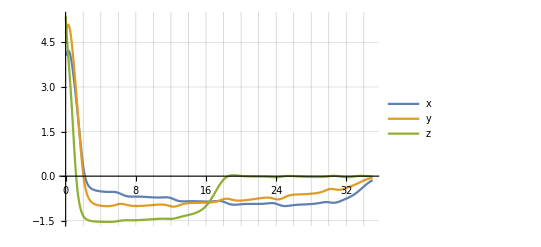
-Graphics-time (s)error(m/s)

```mathematica
errorv:= stateList[[1;;NN,{7,8,9}]]-Table[vd[stepsize (i-1)],{i,1,Length[stateList[[;;,1]]]}];
If[SIMFULLY,
Labeled[
ListLinePlot[{
errorv[[;;,1]],errorv[[;;,2]],errorv[[;;,3]]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","error(m/s)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMFULLY,Export[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/error_velocity.pdf",%];]
```

## Disturbance estimates

```mathematica
(*(bT,BT)*)
estimate[i_]:= estimatorsList[[i,{1,2,3,4,5,6}]];
```

### disturbance bT

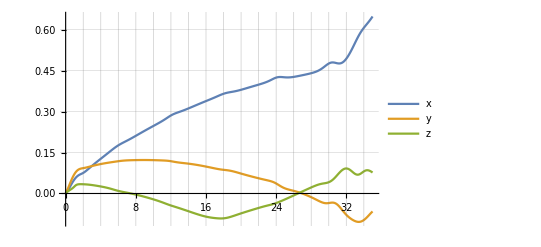
-Graphics-time (s)estimate b_T(N/kg)

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
Table[estimate[i][[1]],{i,1,NN}],
Table[estimate[i][[2]],{i,1,NN}],
Table[estimate[i][[3]],{i,1,NN}]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","estimate b_T(N/kg)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMFULLY,Export[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/bT.pdf",%];]
```

#### note that b != bT

```mathematica
b/.PhysicalConstants
If[SIMFULLY,√(#.#)&[b-estimate[-1][[1;;3]]/.PhysicalConstants]]
If[SIMFULLY,180/π ArcCos[(#/(√(#.#))&[gravity{0,0,1}+ad[NN stepsize]-b]).(#/(√(#.#))&[gravity{0,0,1}+ad[NN stepsize]-estimate[-1][[1;;3]]])]/.PhysicalConstants]
```

{0.693672,0.,-0.693672}

0.774592

0.624263

### disturbance BT

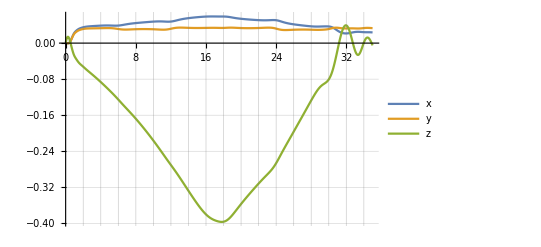
-Graphics-time (s)estimate B_T(N/kg)

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
Table[estimate[i][[4]],{i,1,NN}],
Table[estimate[i][[5]],{i,1,NN}],
Table[estimate[i][[6]],{i,1,NN}]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","estimate B_T(N/kg)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMFULLY,Export[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/BBT.pdf",%];]
```

### note that B != BT

```mathematica
B/.PhysicalConstants
If[SIMFULLY,√(#.#)&[B-estimate[-1][[4;;6]]/.PhysicalConstants]]
If[SIMFULLY,
(#1.#2&[B-estimate[-1][[4;;6]],# ]/.PhysicalConstants)&[
ϕT[f[stateList[[-1,;;]],{pd[NN stepsize],vd[NN stepsize]}][[7;;9]]]/.PhysicalConstants
]
]
```

{-0.0396718,0.654,1.02067}

1.20064

0.759251

## Disturbance estimates

```mathematica
(*(bτ,Bτ)*)
estimate[i_]:= estimatorsList[[i,{7,8,9,10,11,12}]];
```

### disturbance bτ

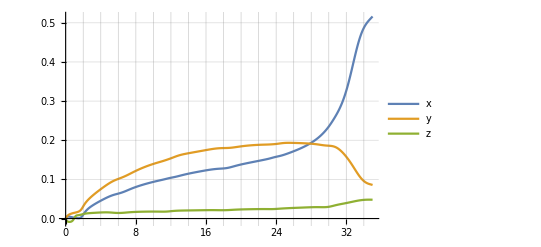
-Graphics-time (s)estimate b_τ(N/kg)

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
Table[estimate[i][[1]],{i,1,NN}],
Table[estimate[i][[2]],{i,1,NN}],
Table[estimate[i][[3]],{i,1,NN}]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","estimate b_τ(N/kg)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMFULLY,Export[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/btau.pdf",%];]
```

#### note that b != bτ

```mathematica
b/.PhysicalConstants
If[SIMFULLY,√(#.#)&[b-estimate[-1][[1;;3]]/.PhysicalConstants]]
If[SIMFULLY,180/π ArcCos[(#/(√(#.#))&[gravity{0,0,1}+ad[NN stepsize]-b]).(#/(√(#.#))&[gravity{0,0,1}+ad[NN stepsize]-estimate[-1][[1;;3]]])]/.PhysicalConstants]
```

{0.693672,0.,-0.693672}

0.767448

1.27528

### disturbance Bτ

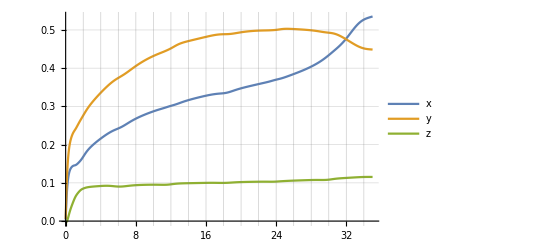
-Graphics-time (s)estimate B_τ(N/kg)

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
Table[estimate[i][[4]],{i,1,NN}],
Table[estimate[i][[5]],{i,1,NN}],
Table[estimate[i][[6]],{i,1,NN}]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","estimate B_τ(N/kg)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMFULLY,Export[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/BBtau.pdf",%];]
```

#### note that B != Bτ

```mathematica
B/.PhysicalConstants
If[SIMFULLY,√(#.#)&[B-estimate[-1][[4;;6]]/.PhysicalConstants]]
If[SIMFULLY,
(#1.#2&[B-estimate[-1][[4;;6]],# ]/.PhysicalConstants)&[
ϕT[f[stateList[[-1,;;]],{pd[NN stepsize],vd[NN stepsize]}][[7;;9]]]/.PhysicalConstants
]
]
```

{-0.0396718,0.654,1.02067}

1.09186

0.649853

## Input

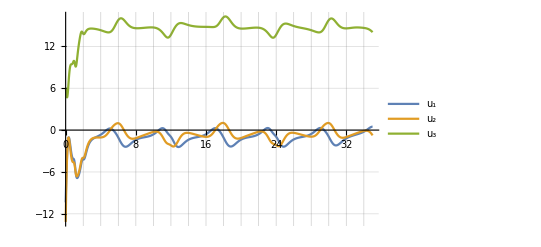
-Graphics-Time (s)(N)

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
inputList[[;;,1]],
inputList[[;;,2]],
inputList[[;;,3]]
},
PlotLegends->Placed[{"u_1","u_2","u_3"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"Time (s)","(N)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMFULLY,Export[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/input.pdf",%];]
```

## Error in state (|z-z^*|) and in input (|u-u^*|)

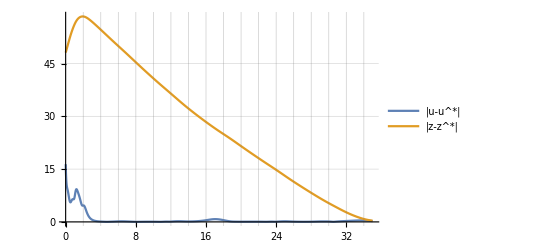
-Graphics-Time (s)

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
Map[Norm,inputList-inputStarList],
Map[Norm,stateList-stateStarList]
},
PlotLegends->Placed[{"|u-u^*|","|z-z^*|"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"Time (s)",""},{Bottom,Left},RotateLabel->True
]
]
If[SIMFULLY,Export[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/errors.pdf",%];]
```

## Lyapunov function

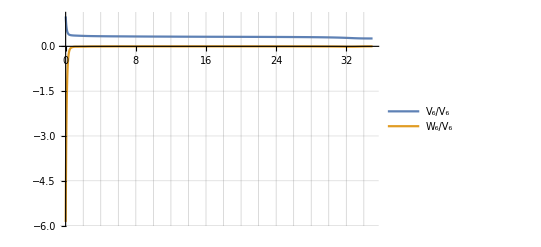
-Graphics-Time (s)

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
VList/VList[[1]],
WList/VList[[1]]
},
PlotLegends->Placed[{"V_6/V_6","W_6/V_6"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"Time (s)",""},{Bottom,Left},RotateLabel->True
]
]
If[SIMFULLY,Export[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/lyapunov_and_derivative.pdf",%];]
```

## Tension function

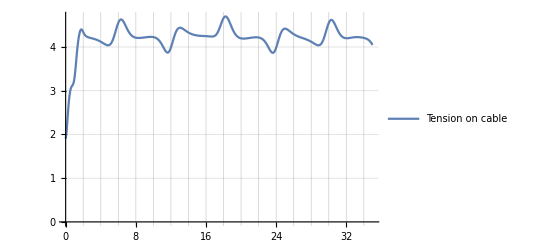
-Graphics-Time (s)(N)

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
tensionsList
},
PlotLegends->Placed[{"Tension on cable"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"Time (s)","(N)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMFULLY,Export[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/tension.pdf",%];]
```

# controller for original system (after backstepping): under-actuated

## state

```mathematica
(*state*)
z2R[]:=Join[zR[],#1/(√(#1.#1)),OP[#1/(√(#1.#1))].#2]&[RandomReal[{-2,2},3],RandomReal[{-2,2},3]]/.PhysicalConstants
(*test*)
If[!COMMENT,z2R[]]
```

{7.99948,-1.9364,3.04395,7.17417,-2.27712,2.40147,1.29294,-2.91169,-7.33411,-5.11962,0.113344,-0.700982,0.00686506,0.642639,0.766139,0.86179,0.485913,-0.415307}

## projection

```mathematica
(*projection*)
Projz2[z2_]:=Join[Projz[z2[[1;;-7]]],#1/(√(#1.#1)),OP[#1/(√(#1.#1))].#2]&[z2[[-6;;-4]],z2[[-3;;-1]]]/.PhysicalConstants
Projz2[#]-#&[z2R[]]//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## open-loop vector field

```mathematica
Z2[z2_,u2_,gravity_,winds_]:=Module[
{
z=z2[[1;;-7]],
(**)
rr=z2[[-6;;-4]],
ωω=z2[[-3;;-1]],

U=u2[[1]],(*thrust*)
ττ=u2[[2;;4]](*angular acceleration*)
},
Join[
Z[z,U rr,gravity,winds],
Skew[ωω].rr,
OP[rr].ττ
]
]
```

## aerial vehicle torque control

```mathematica
τFFBOUND=12;
ωDBOUND=12;
torqueControl[x_,{d0u_,d1u_,d2u_}]:=Module[
{
r=x[[1;;3]],
ω=x[[4;;6]],

τff,τkp,τkd
},
Module[
{
rd=#1/(√(#1.#1))&[d0u],
ωd=Skew[#1/(√(#1.#1))].(#2/(√(#1.#1)))&[d0u,d1u],
τd=Skew[#1/(√(#1.#1))].(#3/(√(#1.#1))-2#2/(#1.#1)(#1.#2)/(√(#1.#1)))&[d0u,d1u,d2u]
},
(*feedforward term*)
τff=OP[r].τd-r.ωd Skew[ω].r;
(*bound feedforward term as precaution*)
τff=#1/(√(1+(#1.#1)/#2^2))&[τff,τFFBOUND];
(*derivative term*)
τkd=-kdUAV(ω-(#1/(√(1+(#1.#1)/#2^2))&[OP[r].ωd,ωDBOUND]));
(*τkd=-kdUAV(ω-OP[r].ωd);*)
(*proportional term*)
τkp=-kpUAV Skew[rd].r;

τff+τkp+τkd
]
]
```

## Input and update-laws combined

```mathematica
InputAndUpdateLaws[t_,z2_,stateController_,{stepsize_,inputs_}]:=Module[{
rr=z2[[-6;;-4]],
ωω=z2[[-3;;-1]],
ττ,

(*x = (p,v,n,ω)*)
x=f[z2[[1;;-7]],Evaluate[{pd[t],vd[t]}]]/.Controllers//N,

bT=stateController[[1;;3]],
BT=stateController[[4;;6]],
bτ=stateController[[7;;9]],
Bτ=stateController[[10;;12]],

g0=Evaluate[gravity{0,0,1}+ad[t]/.Controllers]//N,
g1=Evaluate[jd[t]]//N,
g2=Evaluate[sd[t]]//N,

V6, W6
},
Module[{
p=x[[1;;3]]//N,
v=x[[4;;6]]//N,
n=x[[7;;9]]//N,
ω=x[[10;;12]]//N
},
Module[{
(*x1=Evaluate[Join[p,v,g0]]//N,*)
x2=Evaluate[Join[p,v,g0,n,g1]]//N,
x3 =Evaluate[Join[p,v,g0,n,g1,bT]]//N,
x4 =Evaluate[Join[p,v,g0,n,g1,bT,BT]]//N,
x5 =Evaluate[Join[p,v,g0,n,g1,bT,BT,ω,g2]]//N,
x6 =Evaluate[Join[p,v,g0,n,g1,bT,BT,ω,g2,bτ,Bτ]]//N,
ν,

d0u0,
d1u0,d1u0list,
d2u0,d2u0list
},
Module[{
ωcl=Evaluate[ω2cl[x3]]//N,
dωcl=dω2cl[x3],
(*dωcl=Evaluate[Transpose[Table[D[ω2cl[ReplacePart[x3,i->xlocal]],xlocal]/.{xlocal->x3[[i]] },{i,Range[18]}]]]//N,*)
XbτChosenFast,XBτChosenFast,

bTdot,BTdot,bτdot,Bτdot,
zdot
},

ν=Join[{T3cl[x4]},τ1clAUXILIAR[x5,bτ,Bτ,{ωcl,dωcl}]];
d0u0=uϕ[Join[p,v,n,ω],ν]/.Controllers;


bTdot=EstimatorProj[DiagonalMatrix[kibT].XbTChosenFast[x2,bT],bT,{θ0bT,ϵbT,δbT,nbT}]/.ControllersWithEstimators;
BTdot=EstimatorProj[DiagonalMatrix[kiBT].XBTChosenFast[x3,BT],BT,{θ0BT,ϵBT,δBT,nBT}]/.ControllersWithEstimators;

XbτChosenFast=γω(ω-ωcl).(-#)&[dωcl[[;;,{4,5,6}]]]/.Controllers//N;
bτdot=EstimatorProj[kibτ XbτChosenFast,bτ,{θ0bτ,ϵbτ,δbτ,nbτ}]/.Estimators//N;
XBτChosenFast=γω(ω-ωcl).(ϕτ[n]-KroneckerProduct[#.n, ϕT[n]])&[dωcl[[;;,{4,5,6}]]]/.Controllers//N;
Bτdot=EstimatorProj[kiBτ XBτChosenFast,Bτ,{θ0Bτ,ϵBτ,δBτ,nBτ}]/.Estimators//N;

V6=Subscript[V, 6][x6 ,b/.PhysicalConstants,B/.PhysicalConstants];
(*the one below takes too long: because it recomputes dωcl*)
(*W6=Subscript[W, 6][x6 ,b/.PhysicalConstants,B/.PhysicalConstants];*)
W6=Subscript[W, 5][x5 ,b/.PhysicalConstants,B/.PhysicalConstants]-(((b/.PhysicalConstants)-bτ).(bτdot-kibτ XbτChosenFast))/kibτ-(((B/.PhysicalConstants)-Bτ).(Bτdot-kiBτ XBτChosenFast))/kiBτ/.ControllersWithEstimators;

(*estimating d/dt u*)
d1u0list=Transpose[Join[
{1/stepsize NDSolve`FiniteDifferenceDerivative[Derivative[1],Range[Length[#]],#]&[inputs[[;;,1]]]},
{1/stepsize NDSolve`FiniteDifferenceDerivative[Derivative[1],Range[Length[#]],#]&[inputs[[;;,2]]]},
{1/stepsize NDSolve`FiniteDifferenceDerivative[Derivative[1],Range[Length[#]],#]&[inputs[[;;,3]]]}
]];
(*filter estimate of d/dt u*)
d1u0=Median[d1u0list[[-3;;-1]]];

(*estimating d/dt d/dt u*)
d2u0list=Transpose[Join[
{1/stepsize^2 NDSolve`FiniteDifferenceDerivative[Derivative[2],Range[Length[#]],#]&[inputs[[;;,1]]]},
{1/stepsize^2 NDSolve`FiniteDifferenceDerivative[Derivative[2],Range[Length[#]],#]&[inputs[[;;,2]]]},
{1/stepsize^2 NDSolve`FiniteDifferenceDerivative[Derivative[2],Range[Length[#]],#]&[inputs[[;;,3]]]}
]];
(*filter estimate of d/dt d/dt u*)
d2u0=Median[d2u0list[[-3;;-1]]];

ττ=torqueControl[Join[rr,ωω],{d0u0,d1u0,d2u0}]/.Controllers//N;
{Join[{d0u0.rr},ττ],Join[bTdot,BTdot,bτdot,Bτdot],V6,W6,{d0u0,d1u0,d2u0}}

]
]
]
]
If[!COMMENT,
InputAndUpdateLaws[RandomReal[{-2,2}],z2R[],RandomReal[{-2,2},12],{0.005,ConstantArray[{0,0,1},10]}]//Timing
]
```

{0.208,{{-16.3928,7.82407,1.64651,19.2262},{2.11313,2.14834,-2.15963,1.88814,-2.58275,2.09392,0.549284,-1.65085,0.654736,9.11896,138.898,3.84317},245.954,-7829.02,{{28.8835,46.629,2.74551},{0.,0.,0.},{0.,0.,0.}}}}

## equilibrium z^*, u^*, and verifying (ż)^*=Z(z^*,u^*)

### z^*

```mathematica
z2startrajectory[t_]:=Join[
zstartrajectory[t],
#1/(√(#1.#1)),
Skew[#1/(√(#1.#1))].(#2/(√(#1.#1)))
]&[ustartrajectory[t],(D[ustartrajectory[tt],tt]/.{tt-> t})]
z2startrajectory[RandomReal[]]/.PhysicalConstants//Timing
```

{0.284,{0.754616,1.40514,0.875688,0.618774,1.33481,1.965,0.444241,-0.68553,-0.548236,0.458301,-0.483838,-0.533462,-0.0995222,-0.0907754,0.990886,-0.131686,-0.0544179,-0.0182114}}

### u^*

```mathematica
u2startrajectory[t_]:=Join[
{√(#1.#1)},
Skew[#1/(√(#1.#1))].(#3/(√(#1.#1))-2#2/(√(#1.#1))(#1/(√(#1.#1))).(#2/(√(#1.#1))))
]&[ustartrajectory[t],(D[ustartrajectory[tt],tt]/.{tt-> t}),(D[ustartrajectory[tt],{tt,2}]/.{tt-> t})]
u2startrajectory[RandomReal[]]/.PhysicalConstants//Timing
```

{1.304,{14.2743,-0.282015,-0.130187,-0.0280288}}

### (ż)^*=Z(z^*,u^*) this must be satisfied

```mathematica
error[t_]:=(D[z2startrajectory[tt],tt]/.{tt-> t})-Z2[z2startrajectory[t],u2startrajectory[t],gravity{0,0,1},{w1,w2,w3,W1,W2,W3}]
error[RandomReal[]]/.PhysicalConstants//Chop//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### combine z2^*,u2^* to speed up things

```mathematica
AUX2startrajectory[t_]:={
Join[
zstartrajectory[t],
#1/(√(#1.#1)),
Skew[#1/(√(#1.#1))].(#2/(√(#1.#1)))
],
Join[
{√(#1.#1)},
Skew[#1/(√(#1.#1))].(#3/(√(#1.#1))-2#2/(√(#1.#1))(#1/(√(#1.#1))).(#2/(√(#1.#1))))
]
}&[ustartrajectory[t],(D[ustartrajectory[tt],tt]/.{tt-> t}),(D[ustartrajectory[tt],{tt,2}]/.{tt-> t})]
AUX2startrajectory[RandomReal[]]/.PhysicalConstants//Timing
```

{1.356,{{0.270977,1.62991,1.22934,0.227661,1.45551,2.31456,0.943934,0.0923806,-0.442589,0.653961,0.103281,-0.452412,-0.0218293,-0.119295,0.992619,0.0420178,-0.108418,-0.0121059},{13.9188,-0.0405686,-0.216742,-0.0269407}}}

## Simulation

## initial condition

```mathematica
(*initial state*)
z20=Join[
{7,7,7},(*p*)
{7,7,7}+l{0,0,1},(*P*)
{0,0,0},(*v*)
{0,0,0},(*V*)
{0,0,1},(*r*)
{0,0,0}(*ω*)
]/.PhysicalConstants//N;

(*(*initial state*)
z20=Join[
{0,0,0},(*p*)
{0,0,0}+l{0,0,1},(*P*)
{0,0,0},(*v*)
{0,0,0},(*V*)
{0,0,1},(*r*)
{0,0,0}(*ω*)
]/.PhysicalConstants//N;*)
Projz2[#]-#&[z20]//Chop
(*initial estimators*)
estimators0=ConstantArray[0,12];
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## this is necessary for estimating (d^1 u)/dt^1 and (d^2 u)/dt^2

```mathematica
{input,estimatorsUpdate,V6,W6,{d0u,d1u,d2u}}=InputAndUpdateLaws[0,z20,estimators0,{0.005,ConstantArray[{0,0,1},10]}];
inputs=Table[#,10]&[d0u];
roll[listps_,p0_]:=Join[listps[[2;;-1]],{p0}]
```

## simulation

```mathematica
If[SIMUNDER,
stepsize=0.005;
TFINAL=35;
NN=Round[TFINAL/stepsize];

stateList={};
estimatorsList={};
stateStarList={};
(*inputStarList={};*)
tensionsList={};

inputList ={};
VList ={};
WList ={};

debugList={};
attitudeerrorList={};

kk=1;
i0=1;
For[i=i0,i<=NN,i++,

time=stepsize(i-1);

{input,estimatorsUpdate,V6,W6,{d0u0,d1u0,d2u0}}=InputAndUpdateLaws[time,z20,estimators0,{stepsize,inputs}];


z20=Projz2[z20+stepsize Z2[z20,input,gravity{0,0,1},{w1,w2,w3,W1,W2,W3}/.PhysicalConstants]]/.PhysicalConstants;
estimators0=estimators0+stepsize estimatorsUpdate;

(*update history of inputs -- for the purposes of estimating (d^1 u)/dt^1 and (d^2 u)/dt^2*)
inputs=roll[inputs,d0u0];


debug=Join[d0u0,d1u0,d2u0];
attitudeerror={
1-#1.(#2/(√(#2.#2)))&[z20[[-6;;-4]], d0u0],
√(#.#)&[z20[[-3;;-1]]-OP[z20[[-6;;-4]]].Skew[#1/(√(#1.#1))].(#2/(√(#1.#1)))&[d0u0,d1u0]]
};

debugList=Join[debugList,{debug}];
attitudeerrorList=Join[attitudeerrorList,{attitudeerror}];

stateList= Join[stateList,{z20}];
estimatorsList= Join[estimatorsList,{estimators0}];
inputList= Join[inputList,{input}];

stateStarList= Join[stateStarList,{z2startrajectory[time]/.PhysicalConstants}];
(*inputStarList= Join[inputStarList,{u2startrajectory[time]/.PhysicalConstants}];*)
tensionsList= Join[tensionsList,{Tension[z20[[1;;-7]],d0u0.# #&[z20[[-6;;-4]]],gravity{0,0,1},{w1,w2,w3,W1,W2,W3}]/.PhysicalConstants}];


VList= Join[VList,{V6}];
WList= Join[WList,{W6}];


If[i≥500 kk,Play[Sin[440 2Pi t],{t,0,1}](*Beep[]*);Print[i];kk=kk+1];
]
]
Play[Sin[440 2Pi t],{t,0,1}]
Play[Sin[440 2Pi t],{t,0,1}]
Play[Sin[440 2Pi t],{t,0,1}]
```

500

1000

1500

2000

2500

3000

3500

4000

4500

5000

5500

6000

6500

7000

continue simulation

```mathematica
(*If[SIMUNDER,
stepsize=0.005;
NN=5000+2000;

z20=stateList[[-1,;;]];
i0=i-1;
stateList=stateList[[1;;-2,;;]];
inputList=inputList[[1;;-2,;;]];
estimatorsList=estimatorsList[[1;;-2,;;]];
debugList=debugList[[1;;-2,;;]];
attitudeerrorList=attitudeerrorList[[1;;-2,;;]];

For[i=i0,i<=NN,i++,

time=stepsize(i-1);

{input,estimatorsUpdate,V6,W6,{d0u0,d1u0,d2u0}}=InputAndUpdateLaws[time,z20,estimators0,{stepsize,inputs}];


z20=Projz2[z20+stepsize Z2[z20,input,gravity{0,0,1},{w1,w2,w3,W1,W2,W3}/.PhysicalConstants]]/.PhysicalConstants;
estimators0=estimators0+stepsize estimatorsUpdate;

(*update history of inputs -- for the purposes of estimating (d^1 u)/dt^1 and (d^2 u)/dt^2*)
inputs=roll[inputs,d0u0];


debug=Join[d0u0,d1u0,d2u0];
attitudeerror={
1-#1.#2/(√(#2.#2))&[z20[[-6;;-4]], d0u0],
√(#.#)&[z20[[-3;;-1]]-OP[z20[[-6;;-4]]].Skew[#1/(√(#1.#1))].#2/(√(#1.#1))&[d0u0,d1u0]]
};

debugList=Join[debugList,{debug}];
attitudeerrorList=Join[attitudeerrorList,{attitudeerror}];

stateList= Join[stateList,{z20}];
estimatorsList= Join[estimatorsList,{estimators0}];
inputList= Join[inputList,{input}];


If[i≥400 kk,Play[Sin[440 2Pi t],{t,0,1}](*Beep[]*);Print[i];kk=kk+1];
]
]
Play[Sin[440 2Pi t],{t,0,1}]
Play[Sin[440 2Pi t],{t,0,1}]
Play[Sin[440 2Pi t],{t,0,1}]*)
```

```mathematica
NN=Length[stateList];
XTicksLabels=Table[{Round[1/stepsize]i+1,i},{i,0,TFINAL,2}];
```

## saving data

```mathematica
If[SIMUNDER,
Export[NotebookDirectory[]<>"figures/underactuated/plot_trajectory_matlab/"<>nameSIM<>"/data_physical_constants.txt",ToString[Join[PhysicalConstants0,{timestep-> stepsize}]]];
Export[NotebookDirectory[]<>"figures/underactuated/plot_trajectory_matlab/"<>nameSIM<>"/data_state.mat",stateList];
Export[NotebookDirectory[]<>"figures/underactuated/plot_trajectory_matlab/"<>nameSIM<>"/data_state_star.mat",stateStarList];
(*Export[NotebookDirectory[]<>"figures/underactuated/plot_trajectory_matlab/"<>nameSIM<>"/data_input.mat",inputList];
*)(*Export[NotebookDirectory[]<>"figures/underactuated/plot_trajectory_matlab/"<>nameSIM<>"/data_input_star.mat",inputStarList];*)
]
```

### export

```mathematica
If[SIMUNDER,
Export[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/data_state.mx",stateList];
Export[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/data_estimators.mx",estimatorsList];
Export[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/data_input.mx",inputList];
Export[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/data_statestar.mx",stateStarList];
(*Export[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/data_inputstar.mx",inputStarList];*)
Export[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/data_tension.mx",tensionsList];
Export[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/data_V.mx",VList];
Export[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/data_W.mx",WList];
Export[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/data_debug.mx",debugList];
Export[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/data_attitudeerror.mx",attitudeerrorList];
]
```

### Import

```mathematica
(*stateList=Import[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/data_state.mx"];
estimatorsList=Import[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/data_estimators.mx"];inputList=Import[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/data_input.mx"];
stateStarList=Import[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/data_statestar.mx"];
inputStarList=Import[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/data_inputstar.mx"];
tensionsList=Import[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/data_tension.mx"];
VList=Import[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/data_V.mx"];
WList=Import[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/data_W.mx"];
debugList=Import[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/data_debug.mx"];
attitudeerrorList=Import[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/data_attitudeerror.mx"];
*)
```

## aerial vehicle attitude error

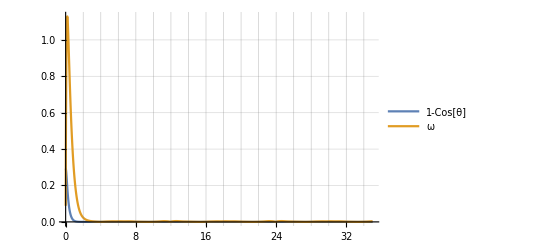
-Graphics-time (s)

```mathematica
If[SIMUNDER,
Labeled[
ListLinePlot[{
attitudeerrorList[[;;,1]],
attitudeerrorList[[;;,2]]
},
PlotLegends->Placed[{"1-Cos[θ]","ω"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)",""},{Bottom,Left},RotateLabel->True
]
]
If[SIMUNDER,Export[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/error_attitude.pdf",%];]
```

## Error position

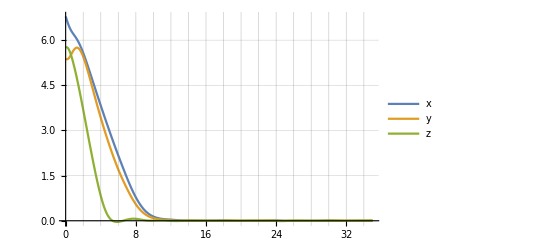
-Graphics-time (s)position error(m)

```mathematica
errorp:= stateList[[;;,{1,2,3}]]-Table[pd[stepsize (i-1)],{i,1,Length[stateList[[;;,1]]]}];
If[SIMUNDER,
Labeled[
ListLinePlot[{
errorp[[;;,1]],errorp[[;;,2]],errorp[[;;,3]]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","position error(m)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMUNDER,Export[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/error_position.pdf",%];]
```

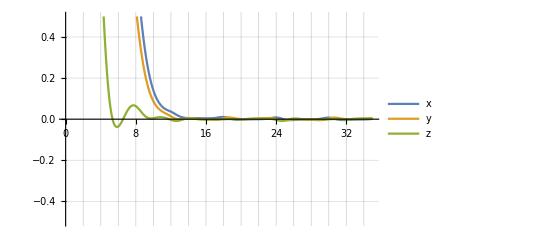
-Graphics-time (s)position error(m)

```mathematica
If[SIMUNDER,
Labeled[
ListLinePlot[{
errorp[[;;,1]],errorp[[;;,2]],errorp[[;;,3]]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->{-0.5,0.5}
],
{"time (s)","position error(m)"},{Bottom,Left},RotateLabel->True
]
]
```

## Error velocity

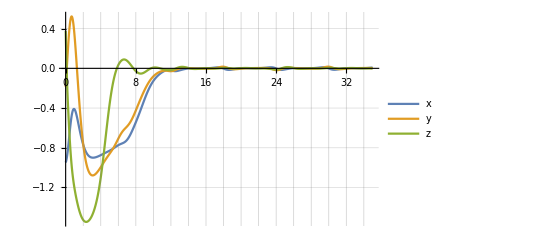
-Graphics-time (s)error(m/s)

```mathematica
errorv:= stateList[[;;,{7,8,9}]]-Table[vd[stepsize (i-1)],{i,1,Length[stateList[[;;,1]]]}];
If[SIMUNDER,
Labeled[
ListLinePlot[{
errorv[[;;,1]],errorv[[;;,2]],errorv[[;;,3]]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","error(m/s)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMUNDER,Export[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/error_velocity.pdf",%];]
```

## Disturbance estimates

```mathematica
(*(bT,BT)*)
estimate[i_]:= estimatorsList[[i,{1,2,3,4,5,6}]];
```

### disturbance bT

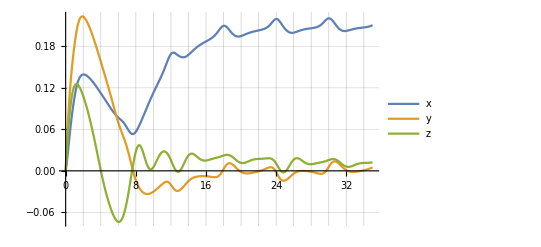
-Graphics-time (s)estimate b_T(N/kg)

```mathematica
If[SIMUNDER,
Labeled[
ListLinePlot[{
Table[estimate[i][[1]],{i,1,NN}],
Table[estimate[i][[2]],{i,1,NN}],
Table[estimate[i][[3]],{i,1,NN}]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","estimate b_T(N/kg)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMUNDER,Export[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/bT.pdf",%];]
```

#### note that b != bT

```mathematica
b/.PhysicalConstants
estimate[-1][[1;;3]]
If[SIMUNDER,√(#.#)&[b-estimate[-1][[1;;3]]/.PhysicalConstants]]
If[SIMUNDER,180/π ArcCos[(#/(√(#.#))&[gravity{0,0,1}+ad[NN stepsize]-b]).(#/(√(#.#))&[gravity{0,0,1}+ad[NN stepsize]-estimate[-1][[1;;3]]])]/.PhysicalConstants]
```

{0.212132,0.,-0.212132}

{0.210613,0.00487203,0.0121384}

0.224329

0.111708

### disturbance BT

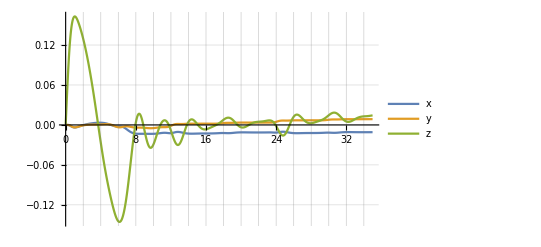
-Graphics-time (s)estimate B_T(N/kg)

```mathematica
If[SIMUNDER,
Labeled[
ListLinePlot[{
Table[estimate[i][[4]],{i,1,NN}],
Table[estimate[i][[5]],{i,1,NN}],
Table[estimate[i][[6]],{i,1,NN}]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","estimate B_T(N/kg)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMUNDER,Export[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/BBT.pdf",%];]
```

#### note that B != BT

```mathematica
B/.PhysicalConstants
If[SIMUNDER,√(#.#)&[B-estimate[-1][[4;;6]]/.PhysicalConstants]]
If[SIMUNDER,
(#1.#2&[B-estimate[-1][[4;;6]],# ]/.PhysicalConstants)&[
ϕT[f[stateList[[-1,;;]],{pd[NN stepsize],vd[NN stepsize]}][[7;;9]]]/.PhysicalConstants
]
]
```

{-0.012132,0.2,0.312132}

0.353976

0.220071

## Disturbance estimates

```mathematica
(*(bτ,Bτ)*)
estimate[i_]:= estimatorsList[[i,{7,8,9,10,11,12}]];
```

### disturbance bτ

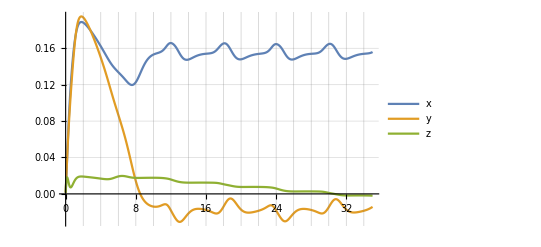
-Graphics-time (s)estimate b_τ(N/kg)

```mathematica
If[SIMUNDER,
Labeled[
ListLinePlot[{
Table[estimate[i][[1]],{i,1,NN}],
Table[estimate[i][[2]],{i,1,NN}],
Table[estimate[i][[3]],{i,1,NN}]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","estimate b_τ(N/kg)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMUNDER,Export[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/btau.pdf",%];]
```

#### note that b != bτ

```mathematica
b/.PhysicalConstants
If[SIMUNDER,√(#.#)&[b-estimate[-1][[1;;3]]/.PhysicalConstants]]
If[SIMUNDER,180/π ArcCos[(#/(√(#.#))&[gravity{0,0,1}+ad[NN stepsize]-b]).(#/(√(#.#))&[gravity{0,0,1}+ad[NN stepsize]-estimate[-1][[1;;3]]])]/.PhysicalConstants]
```

{0.212132,0.,-0.212132}

0.218043

0.449288

### disturbance Bτ

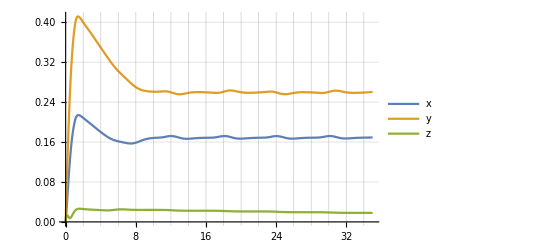
-Graphics-time (s)estimate Disturbance estimates
(B_τ(N/kg)

```mathematica
If[SIMUNDER,
Labeled[
ListLinePlot[{
Table[estimate[i][[4]],{i,1,NN}],
Table[estimate[i][[5]],{i,1,NN}],
Table[estimate[i][[6]],{i,1,NN}]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","estimate Disturbance estimates
(B_τ(N/kg)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMUNDER,Export[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/BBtau.pdf",%];]
```

#### note that B != Bτ

```mathematica
B/.PhysicalConstants
If[SIMUNDER,√(#.#)&[B-estimate[-1][[4;;6]]/.PhysicalConstants]]
If[SIMUNDER,
(#1.#2&[B-estimate[-1][[4;;6]],# ]/.PhysicalConstants)&[
ϕT[f[stateList[[-1,;;]],{pd[NN stepsize],vd[NN stepsize]}][[7;;9]]]/.PhysicalConstants
]
]
```

{-0.012132,0.2,0.312132}

0.350838

0.204177

## Input

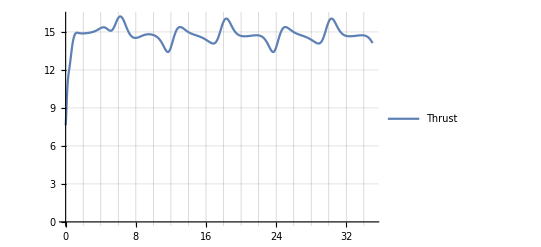
-Graphics-Time (s)(N)

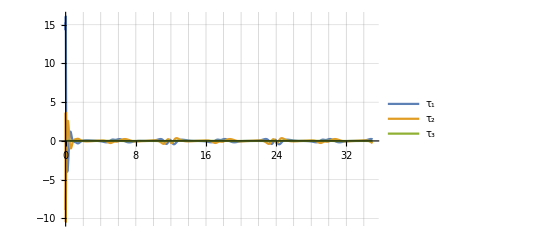
-Graphics-Time (s)(rad/s/s)

```mathematica
If[SIMUNDER,
Labeled[
ListLinePlot[{
inputList[[;;,1]]
},
PlotLegends->Placed[{"Thrust"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"Time (s)","(N)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMUNDER,Export[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/thrust.pdf",%];]
If[SIMUNDER,
Labeled[
ListLinePlot[{
inputList[[;;,2]],
inputList[[;;,3]],
inputList[[;;,4]]
},
PlotLegends->Placed[{"τ_1","τ_2","τ_3"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"Time (s)","(rad/s/s)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMUNDER,Export[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/torque.pdf",%];]
```

## Error in state (|z-z^*|) and in input (|u-u^*|)

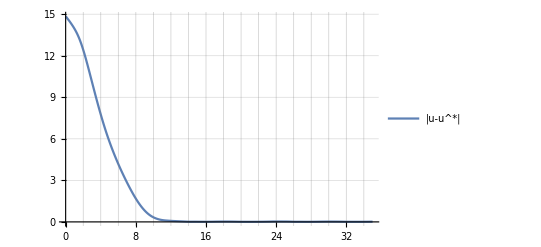
-Graphics-Time (s)

```mathematica
If[SIMUNDER,
Labeled[
ListLinePlot[{
(*Map[Norm,inputList-inputStarList],*)
Map[Norm,stateList-stateStarList]
},
PlotLegends->Placed[{"|u-u^*|","|z-z^*|"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"Time (s)",""},{Bottom,Left},RotateLabel->True
]
]
If[SIMUNDER,Export[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/errors.pdf",%];]
```

## Lyapunov function

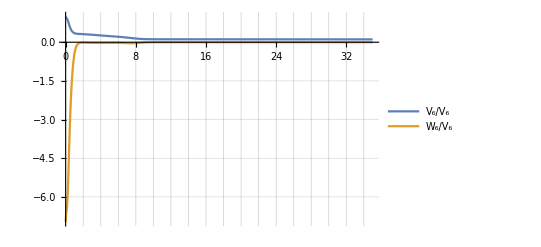
-Graphics-Time (s)

```mathematica
If[SIMUNDER,
Labeled[
ListLinePlot[{
VList/VList[[1]],
WList/VList[[1]]
},
PlotLegends->Placed[{"V_6/V_6","W_6/V_6"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"Time (s)",""},{Bottom,Left},RotateLabel->True
]
]
If[SIMUNDER,Export[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/lyapunov_and_derivative.pdf",%];]
```

## Tension function

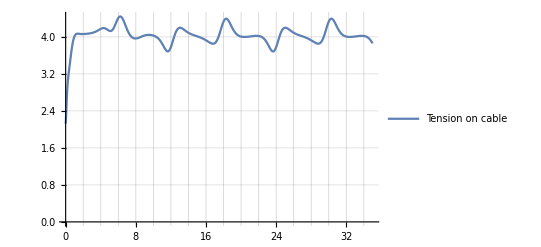
-Graphics-Time (s)(N)

```mathematica
If[SIMUNDER,
Labeled[
ListLinePlot[{
tensionsList
},
PlotLegends->Placed[{"Tension on cable"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"Time (s)","(N)"},{Bottom,Left},RotateLabel->True
]
]
If[SIMUNDER,Export[NotebookDirectory[]<>"figures/underactuated/"<>nameSIM<>"/tension.pdf",%];]
```